# NLS universality class

```mathematica
Quit[];
```

## Focusing NLS - Code by Tom Trogdon

```mathematica
θ[k_,x_,t_]:=2k x+2k^2t;
cc[x_]:=Conjugate[x];
Cs[x_,t_]:=Table[cs[[i]] Exp[I θ[ks[[i]],x,t]],{i,1,Length[ks]}];
iii[x_,t_]:=(Abs[#]>1)&/@Cs[x//N,t//N];
ii[x_,t_]:=Module[{out={},out2={},data,j},
data = iii[x,t];
For[j=1,j≤Length[data],j++,
If[
data[[j]], AppendTo[out,j],AppendTo[out2,j]
];
];
{out,out2}
];
H11[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]]);
];
];
h
];
H22[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]])//cc;
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]])//cc;
];
];
h
];
H12[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(ks[[i]]-cc[ks[[j]]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(ks[[i]]-cc[ks[[j]]]);
];
];
h
];
H21[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(cc[ks[[i]]]-ks[[j]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(cc[ks[[i]]]-ks[[j]]);
];
];
h
];
q[k_,x_,t_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[(k-ks[[is[[j]]]])/(k-cc[ks[[is[[j]]]]]),
{j,1,Length[is]}]
];
quhp[k_,x_,t_,l_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[
If[l≠is[[j]],(k-ks[[is[[j]]]])/(k-cc[ks[[is[[j]]]]]),1/(k-cc[ks[[is[[j]]]]])],
{j,1,Length[is]}]
];
qlhp[k_,x_,t_,l_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[
If[l≠is[[j]],(k-ks[[is[[j]]]])/(k-cc[ks[[is[[j]]]]]),(k-ks[[is[[j]]]])],
{j,1,Length[is]}]
];
diag1[x_,t_]:=Module[{out=ConstantArray[0,Length[ks]],is,isc,i,Cexp,k},
{is,isc} = ii[x,t];
Cexp=Cs[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
out[[i]]=q[ks[[i]],x,t]^2*Cexp[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
out[[i]]=1/(quhp[ks[[i]],x,t,i]^(2)*Cexp[[i]]);
];
out];
diag2[x_,t_]:=Module[{out=ConstantArray[0,Length[ks]],is,isc,i,Cexp,k},
{is,isc} = ii[x,t];
Cexp=Cs[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
out[[i]]=-q[ks[[i]]//cc,x,t]^(-2)*cc[Cexp[[i]]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
out[[i]]=-qlhp[ks[[i]]//cc,x,t,i]^(2)/(cc[Cexp[[i]]]);
];
out];
LS[x_,t_]:=Module[{A,b,diags1,diags2,Ax,b1,b2,is,isc,k,i,H},
diags1=diag1[x,t];
diags2=diag2[x,t];
(*b1 = ConstantArray[0,Length[ks]];b2=b1;
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
b2[[i]]=diags2[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
b1[[i]]=diags1[[i]];
];
b = Join[b1,b2];*)

b1 = ConstantArray[0,Length[ks]];b2=b1;
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
b2[[i]]=1;
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
b1[[i]]=1;
];
b = Join[b1,b2];

H=Join[Join[H11[x,t],H12[x,t],2],Join[H21[x,t],H22[x,t],2]];
A=IdentityMatrix[2Length[ks]]-DiagonalMatrix[Join[diags1,diags2]].H;
{A,DiagonalMatrix[Join[diags1,diags2]].b}
];
sol[x_,t_]:=Module[{A,b,Ax,bx,u,ux,u1,u2,sum,k,i,isc,is},
{A,b}=LS[x,t];
u=LinearSolve[A,b];
u2=u[[Length[ks]+1;;]];
u1=u[[1;;Length[ks]]];
sum = 0;
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
sum = sum + u2[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
sum = sum + u1[[i]];
];
2I sum
];
```

## High precision

```mathematica
sp[x_]:=SetPrecision[x,300]; (* Set code precision to 300 digits*)
```

### PIII - initial data

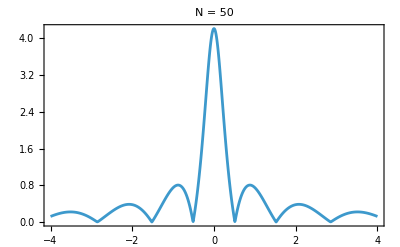

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\50solitonPIII.csv

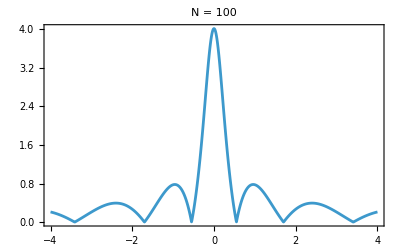

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\100solitonPIII.csv

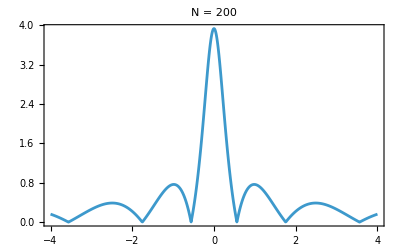

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\200solitonPIII.csv

```mathematica
(*1. Define the Parameter for the Chi Distribution*)
nu=4; 

(*2. Define the analytical mean of the Chi Distribution for muD*)
(*Mean of Chi(nu)=Sqrt[2]*Gamma((nu+1)/2)/Gamma(nu/2)*)
muDCalculated=Sqrt[2]*Gamma[(nu+1)/2]/Gamma[nu/2];

(*4. Loop over the requested Soliton numbers:50,100,200*)
solitonCounts={50,100,200};

Do[(*---A.Setup Parameters for this Iteration---*)
Nsoliton=currentN;
muD=muDCalculated;
(*---B.Generate Random ks---*)
ks=Table[RandomVariate[NormalDistribution[0,15]]+I*RandomVariate[ChiDistribution[nu]],{i,1,Nsoliton}]//sp;
(*---C.Calculate Norming Constants (cs)---*)
cs=Table[Product[ks[[j]]-cc[ks[[n]]],{n,1,Length[ks]}]/Product[ks[[j]]-ks[[n]],{n,1,j-1}]/Product[ks[[j]]-ks[[n]],{n,j+1,Length[ks]}],{j,1,Length[ks]}];
(*---D.Generate Data---*)
data=ParallelTable[{xx,Abs[2/(Nsoliton muD)*sol[(2 xx)/(Nsoliton muD),0]]},{xx,-4,4,1/100}];
(*---E.Plotting (Optional:to see progress)---*)
printPlot=ListPlot[data,Joined->True,PlotRange->All,Axes->False,Frame->True,PlotLabel->Row[{"N = ",Nsoliton}]];
Print[printPlot];
(*---F.Export to CSV---*)
fileName=ToString[Nsoliton]<>"solitonPIII.csv";
path=FileNameJoin[{NotebookDirectory[],fileName}];
Export[path,data];
Print["Exported: ",path];,{currentN,solitonCounts} (*End of Do Loop*)];
```

### PV - Initial data

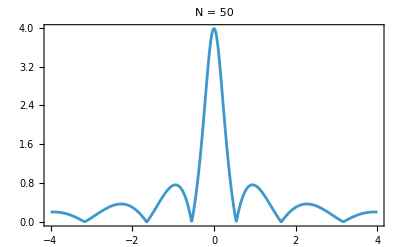

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\50solitonPV.csv

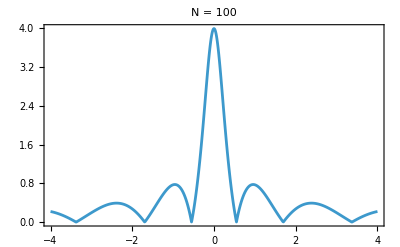

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\100solitonPV.csv

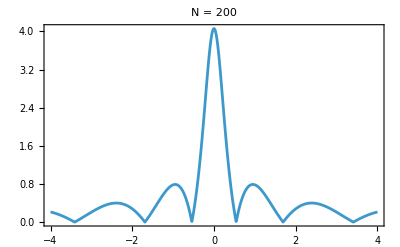

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\200solitonPV.csv

```mathematica
(*1. Define the Parameter for the Chi Distribution and zeta*)
nu=4; 
ζ=0.3;
(*2. Define the analytical mean of the Chi Distribution for muD*)
(*Mean of Chi(nu)=Sqrt[2]*Gamma((nu+1)/2)/Gamma(nu/2)*)
muDCalculated=Sqrt[2]*Gamma[(nu+1)/2]/Gamma[nu/2];

(*4. Loop over the requested Soliton numbers:50,100,200*)
solitonCounts={50,100,200};

Do[(*---A.Setup Parameters for this Iteration---*)
Nsoliton=currentN;
muD=muDCalculated;
(*---B.Generate Random ks---*)
ks=Table[RandomVariate[NormalDistribution[0,15]]+ζ *i +I*RandomVariate[ChiDistribution[nu]],{i,1,Nsoliton}]//sp;
(*---C.Calculate Norming Constants (cs)---*)
cs=Table[Product[ks[[j]]-cc[ks[[n]]],{n,1,Length[ks]}]/Product[ks[[j]]-ks[[n]],{n,1,j-1}]/Product[ks[[j]]-ks[[n]],{n,j+1,Length[ks]}],{j,1,Length[ks]}];
(*---D.Generate Data---*)
data=ParallelTable[{xx,Abs[2/(Nsoliton muD)*sol[(2 xx)/(Nsoliton muD),0]]},{xx,-4,4,1/100}];
(*---E.Plotting (Optional:to see progress)---*)
printPlot=ListPlot[data,Joined->True,PlotRange->All,Axes->False,Frame->True,PlotLabel->Row[{"N = ",Nsoliton}]];
Print[printPlot];
(*---F.Export to CSV---*)
fileName=ToString[Nsoliton]<>"solitonPV.csv";
path=FileNameJoin[{NotebookDirectory[],fileName}];
Export[path,data];
Print["Exported: ",path];,{currentN,solitonCounts} (*End of Do Loop*)];
```

```mathematica
muDCalculated=Sqrt[2]*Gamma[(nu+1)/2]/Gamma[nu/2]
```

```mathematica
2*(3 √(π/2))/2
```

3 √(π/2)

```mathematica
N[3 √(π/2)]
```

3.75994

```mathematica
N[muDCalculated]
```

1.87997

### PIII data with averages

N=50 | Trial 1/10 exported.

N=50 | Trial 2/10 exported.

N=50 | Trial 3/10 exported.

N=50 | Trial 4/10 exported.

N=50 | Trial 5/10 exported.

N=50 | Trial 6/10 exported.

N=50 | Trial 7/10 exported.

N=50 | Trial 8/10 exported.

N=50 | Trial 9/10 exported.

N=50 | Trial 10/10 exported.

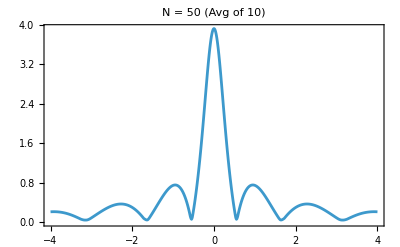

Final Average Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\50solitonPIII_AVERAGED.csv

---------------------------------------

N=100 | Trial 1/10 exported.

N=100 | Trial 2/10 exported.

N=100 | Trial 3/10 exported.

N=100 | Trial 4/10 exported.

N=100 | Trial 5/10 exported.

N=100 | Trial 6/10 exported.

N=100 | Trial 7/10 exported.

N=100 | Trial 8/10 exported.

N=100 | Trial 9/10 exported.

N=100 | Trial 10/10 exported.

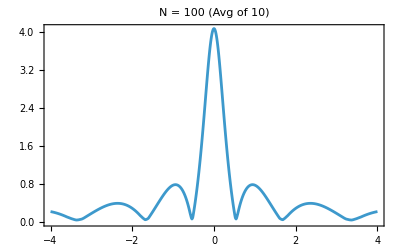

Final Average Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\100solitonPIII_AVERAGED.csv

---------------------------------------

N=200 | Trial 1/10 exported.

N=200 | Trial 2/10 exported.

N=200 | Trial 3/10 exported.

N=200 | Trial 4/10 exported.

N=200 | Trial 5/10 exported.

N=200 | Trial 6/10 exported.

N=200 | Trial 7/10 exported.

N=200 | Trial 8/10 exported.

N=200 | Trial 9/10 exported.

N=200 | Trial 10/10 exported.

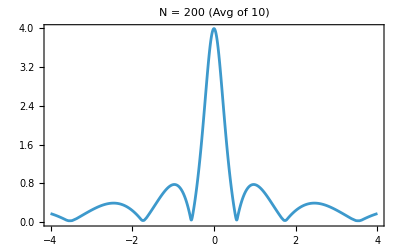

Final Average Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\200solitonPIII_AVERAGED.csv

---------------------------------------

```mathematica
(*1. Setup Parameters*)nu=4;
muDCalculated=Sqrt[2]*Gamma[(nu+1)/2]/Gamma[nu/2];
solitonCounts={50,100,200};

(*NEW:Define how many realizations to average over*)
numRealizations=10;

(*---Main Loop over Soliton Numbers (N)---*)
Do[Nsoliton=currentN;
muD=muDCalculated;
(*Initialize a list to accumulate the y-values for averaging later.*)(*The size 801 comes from Range[-4,4,1/100]*)accumulatedY=ConstantArray[0.0,801];
(*---Inner Loop over Realizations (Trials)---*)Do[(*A.Generate Random ks*)ks=Table[RandomVariate[NormalDistribution[0,15]]+I*RandomVariate[ChiDistribution[nu]],{i,1,Nsoliton}]//sp;
(*B.Calculate Norming Constants (cs)*)cs=Table[Product[ks[[j]]-cc[ks[[n]]],{n,1,Length[ks]}]/Product[ks[[j]]-ks[[n]],{n,1,j-1}]/Product[ks[[j]]-ks[[n]],{n,j+1,Length[ks]}],{j,1,Length[ks]}];
(*C.Generate Data for this Trial*)(*Note:Assuming'sol' function is defined elsewhere in your notebook*)data=ParallelTable[{xx,Abs[2/(Nsoliton muD)*sol[(2 xx)/(Nsoliton muD),0]]},{xx,-4,4,1/100}];
(*D.Accumulate Data for Averaging*)(*We add the y-values (Part 2 of data) to our running total*)accumulatedY=accumulatedY+data[[All,2]];
(*E.Export Intermediate Trial Data*)fileNameTrial=ToString[Nsoliton]<>"solitonPIII_trial"<>ToString[trial]<>".csv";
pathTrial=FileNameJoin[{NotebookDirectory[],fileNameTrial}];
Export[pathTrial,data];
(*Optional:Print progress for individual trials*)Print["N=",Nsoliton," | Trial ",trial,"/",numRealizations," exported."];,{trial,1,numRealizations}];(*End of Inner Loop*)(*---Calculate Average and Export Final---*)(*1. Compute average Y*)averagedY=accumulatedY/numRealizations;
(*2. Reconstruct the dataset using the same x-grid*)xGrid=Range[-4,4,1/100];
finalAveragedData=Transpose[{xGrid,averagedY}];
(*3. Plot the Averaged Result*)printPlot=ListPlot[finalAveragedData,Joined->True,PlotRange->All,Axes->False,Frame->True,PlotLabel->Row[{"N = ",Nsoliton," (Avg of ",numRealizations,")"}]];
Print[printPlot];
(*4. Export Averaged Data*)fileNameAvg=ToString[Nsoliton]<>"solitonPIII_AVERAGED.csv";
pathAvg=FileNameJoin[{NotebookDirectory[],fileNameAvg}];
Export[pathAvg,finalAveragedData];
Print["Final Average Exported: ",pathAvg];
Print["---------------------------------------"];,{currentN,solitonCounts}];
```

### P-V average

N=50 | Trial 1 exported.

N=50 | Trial 2 exported.

N=50 | Trial 3 exported.

N=50 | Trial 4 exported.

N=50 | Trial 5 exported.

N=50 | Trial 6 exported.

N=50 | Trial 7 exported.

N=50 | Trial 8 exported.

N=50 | Trial 9 exported.

N=50 | Trial 10 exported.

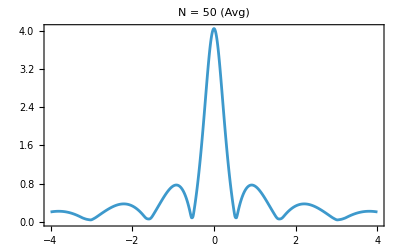

Final Average Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\50solitonPV_AVERAGED.csv

---------------------------------------

N=100 | Trial 1 exported.

N=100 | Trial 2 exported.

N=100 | Trial 3 exported.

N=100 | Trial 4 exported.

N=100 | Trial 5 exported.

N=100 | Trial 6 exported.

N=100 | Trial 7 exported.

N=100 | Trial 8 exported.

N=100 | Trial 9 exported.

N=100 | Trial 10 exported.

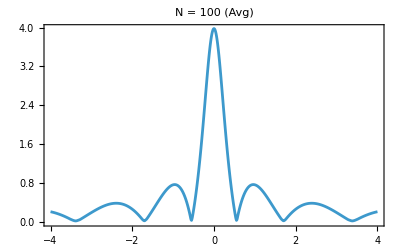

Final Average Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\100solitonPV_AVERAGED.csv

---------------------------------------

N=200 | Trial 1 exported.

N=200 | Trial 2 exported.

N=200 | Trial 3 exported.

N=200 | Trial 4 exported.

N=200 | Trial 5 exported.

N=200 | Trial 6 exported.

N=200 | Trial 7 exported.

$Aborted

```mathematica
(*1. Setup Parameters*)nu=4;
muDCalculated=Sqrt[2]*Gamma[(nu+1)/2]/Gamma[nu/2];
solitonCounts={200};
ζ=0.3;

(*NEW:Define how many realizations to average over*)
numRealizations=10;

Do[(*---A.Setup Parameters for this N---*)Nsoliton=currentN;
muD=muDCalculated;
(*Initialize Accumulator for the Averaging*)(*Grid is-4 to 4 step 0.01=801 points*)accumulatedY=ConstantArray[0.0,801];
(*---B.Inner Loop:Realizations---*)Do[(*Generate Random ks with Zeta shift*)ks=Table[RandomVariate[NormalDistribution[0,15]]+ζ*i+I*RandomVariate[ChiDistribution[nu]],{i,1,Nsoliton}]//sp;
(*Calculate Norming Constants (cs)*)cs=Table[Product[ks[[j]]-cc[ks[[n]]],{n,1,Length[ks]}]/Product[ks[[j]]-ks[[n]],{n,1,j-1}]/Product[ks[[j]]-ks[[n]],{n,j+1,Length[ks]}],{j,1,Length[ks]}];
(*Generate Data*)data=ParallelTable[{xx,Abs[2/(Nsoliton muD)*sol[(2 xx)/(Nsoliton muD),0]]},{xx,-4,4,1/100}];
(*Accumulate for Average*)accumulatedY=accumulatedY+data[[All,2]];
(*---C.Export Intermediate Trial---*)fileNameTrial=ToString[Nsoliton]<>"solitonPV_trial"<>ToString[trial]<>".csv";
pathTrial=FileNameJoin[{NotebookDirectory[],fileNameTrial}];
Export[pathTrial,data];
(*Progress Print*)Print["N=",Nsoliton," | Trial ",trial," exported."];,{trial,1,numRealizations}];(*End Inner Loop*)(*---D.Calculate Average and Export Final---*)(*Compute Mean*)averagedY=accumulatedY/numRealizations;
(*Rebuild Grid {-4,4,0.01}*)xGrid=Range[-4,4,1/100];
finalAveragedData=Transpose[{xGrid,averagedY}];
(*Plot Average*)printPlot=ListPlot[finalAveragedData,Joined->True,PlotRange->All,Axes->False,Frame->True,PlotLabel->Row[{"N = ",Nsoliton," (Avg)"}]];
Print[printPlot];
(*Export Average*)fileNameAvg=ToString[Nsoliton]<>"solitonPV_AVERAGED.csv";
pathAvg=FileNameJoin[{NotebookDirectory[],fileNameAvg}];
Export[pathAvg,finalAveragedData];
Print["Final Average Exported: ",pathAvg];
Print["---------------------------------------"];,{currentN,solitonCounts}];
```